# CoffeeCode Mathematica

CoffeeCode Mathematica Interface, © 2019 Johannes Bausch
For joint Graph State project with Felix Leditzky

This file can be exported as a module, and then imported in a script.

# CoffeeCode Interface

## Setup [Build paths to be fixed here; contains more instructions]

### Paths and Unicorns

These lines HAVE TO BE MODIFIED.

Edit scripts/make-build-dir.sh to activate a valid build environment for building with a modern gcc (>8.2). You can remove all the conda... blabla lines there if the compilation environment is installed globally anyhow. The options you pass to cmake there have to match those that you would pick when setting up a solver directory manually with ccmake. This also includes setting the paths for the boost and nauty libraries (via the options -D PATH_BOOST=/path/to/boost -D PATH_NAUTY=/path/to/nauty).

```mathematica
Clear[CurrentDir]
CurrentDir:=If[$InputFileName≠"",DirectoryName[$InputFileName],NotebookDirectory[]]
```

```mathematica
(* fix paths in this file *)
Get["CCInterfacePaths.m",Path->CurrentDir];
```

```mathematica
(* execute this cell to open the build script for manual editing *)
SystemDialogInput["FileOpen",PARALLELBUILDSETUPSCRIPT]
```

### Build Environments

```mathematica
On[Assert];(* enable sanity checks instead of failing silently *)
```

```mathematica
(* avoid race conditions when building in parallel *)
Clear[ParallelBuildDirectory]
ParallelBuildDirectory[]:=Module[{
targetFolder=PARALLELBUILDPATH<>"release-"<>ToString@$SessionID<>"."<>ToString@$KernelID<>"/"
},
If[!DirectoryQ[targetFolder],
Echo["setting up parallel build directory: "<>targetFolder];
RunProcess[{PARALLELBUILDSETUPSCRIPT,targetFolder}] (* bug with commands like "source" *)
];
targetFolder
]
```

```mathematica
ParallelBuildDirectory[]
```

```mathematica
Clear[BuglessRunProcess]
BuglessRunProcess[exec_String,what_,input_String:"",opts:OptionsPattern[]]:=Module[{
process=StartProcess[exec,opts],
out
},
If[input≠"",WriteLine[process,input]];
While[ProcessStatus[process,"Running"],Pause[1]];
out=ReadString[process];
<|
"ExitCode"->ProcessInformation[process]["ExitCode"],
"StandardError"->"",
"StandardOutput"->out
|>
]

Unprotect[StringForm];
StringForm[a_,b_Parallel`Kernels`kernel]:=""
```

## Basic Graph Functionality [install IGraphM once below, then forget]

### IGraphM

Uncomment the last line in the following cell, then execute to install IGraphM. This only has to be done once per machine.

```mathematica
updateIGraphM[]:=Module[{json,download,target,msg},Check[json=Import["https://api.github.com/repos/szhorvat/IGraphM/releases","JSON"];
download=Lookup[First@Lookup[First[json],"assets"],"browser_download_url"];
msg="Downloading IGraph/M "<>Lookup[First[json],"tag_name"]<>" ...";
target=FileNameJoin[{CreateDirectory[],"IGraphM.paclet"}];
If[$Notebooks,PrintTemporary@Labeled[ProgressIndicator[Appearance->"Necklace"],msg,Right],Print[msg]];
URLSave[download,target],Return[$Failed]];
If[FileExistsQ[target],PacletManager`PacletInstall[target],$Failed]]
(*updateIGraphM[]*) (* uncomment this once and run to install IGraphM locally, then comment again *)
```

```mathematica
Needs["IGraphM`"]
ParallelNeeds["IGraphM`"];
```

### Group for Graph State

GroupForGraph gives the full automorphism group of the underlying graph; we color the environment vertices in a different color to make sure the permutation group will be a product across this partitioning.

```mathematica
Clear[GroupForGraph]
GroupForGraph[graph_Graph,kSys_Integer,extraStabilizedVertices_List:{}]:=GroupForGraph[graph,kSys,extraStabilizedVertices]=With[{
kTot=VertexCount@graph,
(* {1,3,11} for a graph of size 14 would be mapped to {1,0,2,0,0,0,0,0,0,0,3,0,0,0} *)
extraColors=Normal@SparseArray[Thread[extraStabilizedVertices->Range@Length@extraStabilizedVertices],VertexCount@graph]
},
PermutationGroup[
PermutationCycles/@IGBlissAutomorphismGroup[{graph,"VertexColors"->ConstantArray[0,kSys]~Join~ConstantArray[kTot^2,kTot-kSys]+extraColors}]
]
]
```

```mathematica
(* for iterating over tuples, we'll only need the system vertices subgroup, not the full group *)
```

```mathematica
Clear[Subgroup]
Subgroup[group_PermutationGroup,kSys_Integer]:=Subgroup[group,kSys]=group/.{p_Integer/;p>kSys->Nothing}/.Cycles[{}]->Nothing
```

### Plot Environment Vertices in Red

```mathematica
Clear[EnvironmentPlot]
EnvironmentPlot[g_Graph,systemSize_]:=Graph[g,VertexStyle->(
Thread[(Range[VertexCount@g-systemSize]+systemSize)->Red]
),VertexSize->.2,VertexLabels->None]
```

### Create all Possible Choices of Hairs to the Environment

```mathematica
Clear[IsomorphicHairChoiceQ,HairColoring]
HairColoring[hairs_]:=HairColoring[Sort@hairs]=Length/@GroupBy[hairs,Identity]
IsomorphicHairChoiceQ[g_Graph,hairs1_,hairs2_]:=IsomorphicHairChoiceQ[g,hairs1,hairs2]=IsomorphicHairChoiceQ[g,hairs2,hairs1]=IGBlissIsomorphicQ[
{g,"VertexColors"->HairColoring@hairs1},
{g,"VertexColors"->HairColoring@hairs2}
]
IsomorphicHairChoiceQ[g_Graph]:=IsomorphicHairChoiceQ[g,#1,#2]&
```

```mathematica
Clear[HairGraph,AllHairGraphs]
HairGraph[g_Graph,hairs_]:=HairGraph[g,hairs]=With[{
new=VertexCount@g+Range@Length@hairs
},
EdgeList[g]~Join~Thread[hairs<->new]//Graph
]
AllHairGraphs[g_Graph,generator_:Hold[Subsets[#]⟦2;;⟧&]]:=AllHairGraphs[g,generator]=With[{
(* first check for graph isomorphism using a vertex coloring *)
uniqueHairEndpoints=DeleteDuplicates[
ReleaseHold[generator][VertexList@g],
IsomorphicHairChoiceQ[g]
]
},
EnvironmentPlot[HairGraph[g,#],VertexCount@g]&/@uniqueHairEndpoints
]
```

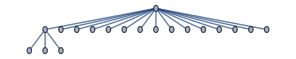
```mathematica
AllHairGraphs[-Graphics-,Subsets[#,{1}]&]
```

### Strong Generating Set Transversal

```mathematica
Clear[SGSTransversal]
(* the head element of the group stabilizer chain already delivers a transversal of a strong generating set *)
SGSTransversal[group_PermutationGroup]:=With[{
chain=GroupStabilizerChain[group]
},
Partition[chain,2,1]/.{Rule[sA_,gA_],Rule[sB_,gB_]}:>(
Complement[sB,sA]->PermutationGroup@Complement[GroupGenerators@gA,GroupGenerators@gB]
)/.{Rule[s_,PermutationGroup[{}]]:>Nothing}
]
```

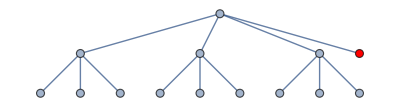
```mathematica
SGSTransversal[GroupForGraph[-Graphics-,13]]
```

### Detecting Products of Symmetric Groups

```mathematica
Clear[ProductOfSymmetricGroupsQ]
ProductOfSymmetricGroupsQ[group_PermutationGroup]:=With[{
orbits=GroupOrbits@group
},
(GroupOrder/@(
GroupStabilizer[group,Complement[Flatten@orbits,#]]&/@orbits
)
)==(Factorial/@Length/@orbits)
]
```

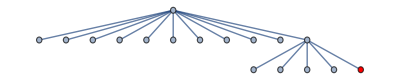
```mathematica
GroupForGraph[-Graphics-,16]
ProductOfSymmetricGroupsQ@%
GroupOrbits@%%
```

```mathematica
GroupForGraph[-Graphics-,13]
ProductOfSymmetricGroupsQ@%
```

```mathematica
Clear[CanonicalizeByOrbits]
(* sort graph vertices such that environment all the way to the right, and orbits of size > 1 come up first *)
CanonicalizeByOrbits[graph_Graph,kSys_Integer,extraStabilizedVertices_List:{}]:=With[{
orbits=GroupOrbits[GroupForGraph[graph,kSys,extraStabilizedVertices],Range@VertexCount@graph],
kTot=VertexCount@graph
},

With[{
coloring=Thread/@MapIndexed[Function[{orbit,i},
(* environment last, length 1 next, nontrivial orbits first; stable sort so add i *)
If[Min@orbit>kSys,
orbit->10kTot+First@i,
If[Length@orbit==1,
orbit->5kTot+First@i,
orbit->First@i
]]
],orbits]//Flatten//SortBy[First]
},
Graph[
IGBlissCanonicalGraph[{graph,"VertexColors"->Last/@coloring}],
VertexLabels->"Index"
]
]
]
```

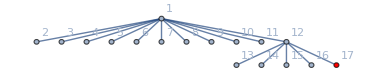
```mathematica
CanonicalizeByOrbits[-Graphics-,16]
```

### Detecting Multiple Hairs per Orbit

```mathematica
Clear[OrbitsHaveMultipleHairsQ]
OrbitsHaveMultipleHairsQ[group_PermutationGroup,g_Graph,kSys_Integer]:=Module[{
environmentVertices=VertexList[g]⟦kSys+1;;⟧,
hairNeighbourIndices
},
hairNeighbourIndices=VertexIndex[g,#]&/@VertexList@Subgraph[NeighborhoodGraph[g,environmentVertices],Complement[VertexList@g,environmentVertices]];

Intersection[#,hairNeighbourIndices]&/@GroupOrbits[group]//AnyTrue[#,Length@##>1&]&
]
```

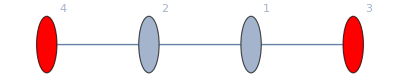
```mathematica
-Graphics-
Subgroup[GroupForGraph[%,2],2]
OrbitsHaveMultipleHairsQ[%,%%,2]
```

## CoffeeCode Link [See individual sections for tests]

```mathematica
CCCUSTOMINSTANCEFILE="cc-instance-custom.h";
```

### Exporting MM symbols

```mathematica
Clear[ExportAdjacencyMatrix]
ExportAdjacencyMatrix[g_Graph]:=With[{
Avec=g//AdjacencyMatrix//Normal//Flatten
},
StringJoin[ToString/@Avec]
]
```

```mathematica
Clear[SGSTransversalMMForm]
SGSTransversalMMForm[list_List,kSys_Integer]:=list/.{
Rule[{idx_Integer},PermutationGroup[cycles_List]]:>Module[{
permutationIndices=PermutationList[#,kSys]&/@cycles
},

(* the pivot point is the first index for which the SGSGenerator acts nontrivially on (so one point past the points that are stabilized).
If the pivot point for the SGSGenerator is 2, that means we want to check indices 0 and 1 in C++; in MM this would correspond to indices {1, 2}, which is what ⟦;;2⟧ truncates to.
Therefore we validly don't subtract 1 from the pivot point, but do subtract 1 from all other indices *)
StringRiffle[Flatten@{
"\tSGSGenerator<"<>ToString@(#1)<>", Group<",
("\t\tPermutation<"<>StringRiffle[ToString/@(##-1),","]<>">")&/@#2,
"\t>>"
},"\n"]&@@{idx,permutationIndices}

]
}//Flatten//("using sgs = SGSTransversal<\n"<>StringRiffle[#,",\n"]<>"\n>;")&

(* for the trivial transversal we simply pass an orbit, sort the graph canonically etc *)
Clear[TrivialSGSTransversalMMForm]
TrivialSGSTransversalMMForm[list_List,kSys_Integer]:=With[{
orbits=list/.{n_Integer}:>Nothing//SortBy[First]
},
With[{
lengths=Accumulate[Length/@orbits]
},
With[{
orbitBounds={0}~Join~lengths//Partition[#,2,1]&
},

StringRiffle[(
"\tTrivialSGSOrbit<"<>ToString[#1]<>", "<>ToString[#2]<>">"
)&@@@orbitBounds,
",\n"]
]//("using sgs = TrivialSGSTransversal<"<>ToString[kSys]<>",\n"<>#<>"\n>;")&
]
]
```

```mathematica
Subgroup[GroupForGraph[-Graphics-,2],2]
TrivialSGSTransversalMMForm[GroupOrbits@%,2]
```

```mathematica
Clear[ExportSymmetricCCInstance]
ExportSymmetricCCInstance[graph_Graph,kSys_Integer,extraStabilizedVertices_List:{},name_:"graphstate_instance"]:=With[{
group=Subgroup[GroupForGraph[graph,kSys,extraStabilizedVertices],kSys],
kTot=VertexCount@graph
},

If[!OrbitsHaveMultipleHairsQ[group,graph,kSys]∧ProductOfSymmetricGroupsQ@group,
(* write Orbits as expected for TrivialSGS Solver *)
With[{
orbits=GroupOrbits@group,
graphCanonicalized=CanonicalizeByOrbits[graph,kSys,extraStabilizedVertices]
},

If[Length@orbits==0∨Max[Length/@orbits]==1,Echo["WARN: symmetry group is 0. Not a valid symmetric problem instance."];Throw["invalid instance"]
];
(*Echo["Product symmetry group with single hairs detected. Compiling for trivial canonical image provider."];*)

"struct "<>name<>" {\n"<>
TrivialSGSTransversalMMForm[orbits,kSys]<>"\n"<>
"constexpr static size_t k_sys = "<>ToString[kSys]<>", k_env = "<>ToString[kTot-kSys]<>";\n"<>
"constexpr static AdjacencyMatrixT<"<>ToString[kTot]<>"> adjacency_matrix{"<>ToString[Normal@AdjacencyMatrix@graphCanonicalized]<>"};\n"<>
"};"
]
,
(* write SGSGenerators as expected for Nauty *)
With[{
sgs=SGSTransversal@group
},

If[Length@sgs==0,Echo["WARN: symmetry group is 0. Not a valid symmetric problem instance."];
Throw["invalid instance"]
];
Echo["Nested symmetry group or multiple hairs per orbit detected. Compiling for nauty's canonical image provider."];

"struct "<>name<>" {\n"<>
SGSTransversalMMForm[sgs,kSys]<>"\n"<>
"constexpr static size_t k_sys = "<>ToString[kSys]<>", k_env = "<>ToString[kTot-kSys]<>";\n"<>
"constexpr static AdjacencyMatrixT<"<>ToString[kTot]<>"> adjacency_matrix{"<>ToString[Normal@AdjacencyMatrix@graph]<>"};\n"<>
"};"
]
]
]
```

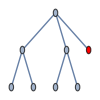
```mathematica
(* can enforce to use the non-nauty symmetric solver by flagging certain vertices as not symmetric *)ExportSymmetricCCInstance[-Graphics-,7,{2}]
```

### Build Interface

```mathematica
Clear[MakeCC]
MakeCC[kSys_Integer,kEnv_Integer]:=With[{
out=RunProcess[
{
"make",
"-B",
"K_SYS="<>ToString@kSys,
"K_ENV="<>ToString@kEnv
},
ProcessDirectory->ParallelBuildDirectory[]
]
},
If[StringTrim@out["StandardError"]≠"",Echo[out["StandardError"]]];
If[out["ExitCode"]≠0(*∨out["StandardError"]≠""*),Echo[out];Throw["make error"]];
]
MakeCC[graph_Graph,kSys_Integer,extraStabilizedVertices_List:{}]:=With[{
instanceFileContent=ExportSymmetricCCInstance[graph,kSys,extraStabilizedVertices]
},

Export[ParallelBuildDirectory[]<>CCCUSTOMINSTANCEFILE,instanceFileContent,"Text"];
MakeCC[kSys,VertexCount@graph-kSys]
]
```

```mathematica
(* this fails if the folder is not already existent MakeCC[9,1] *)
```

```mathematica
MakeCC[-Graphics-,7]
```

```mathematica
Clear[RunCC]
RunCC[graph_Graph,kSys_Integer,extraStabilizedVertices:_List:{}]:=With[{},
If[!MakeCC[graph,kSys,extraStabilizedVertices],Return[False]];

With[{
ccResult=BuglessRunProcess["CoffeeCode",All,ProcessDirectory->ParallelBuildDirectory[]]
},
If[ccResult["ExitCode"]≠0∨ccResult["StandardError"]≠"",Echo[ccResult];Throw["run error"]];

ImportString[ccResult["StandardOutput"],"RawJSON"]
]
]
```

```mathematica
RunCC[-Graphics-,7,{2}]
```

### Full Solver Interface

```mathematica
Clear[CCPath]
CCPath[kSys_Integer,kEnv_Integer]:=CCPath[kSys,kEnv]=CCRELEASEPATHFULLSOLVER<>"CoffeeCode."<>ToString[kSys]<>"."<>ToString[kEnv]

(* RunCC overload *)
RunCC[graph_Graph,kSys_Integer,"Full",extraStabilizedVertices_List:{}(*ignored*)]:=Module[{
adjacencyMatrix=ExportAdjacencyMatrix@graph,
kEnv=VertexCount@graph-kSys
},
With[{
executable=CCPath[kSys,kEnv]
},

Assert[FileExistsQ[executable]];

With[{
ccResult=BuglessRunProcess[executable,All,adjacencyMatrix]
},
If[ccResult["ExitCode"]≠0∨ccResult["StandardError"]≠"",Echo[ccResult];Throw["run error"]];

ImportString[ccResult["StandardOutput"],"RawJSON"]
]
]
]
```

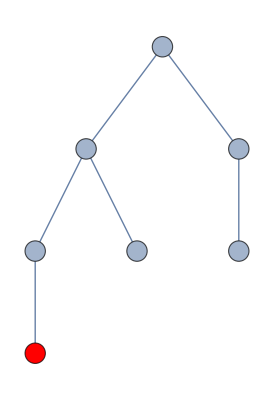
```mathematica
RunCC[-Graphics-,6,"Full"]
```

### Importing JSON format

```mathematica
Clear[CoeffArrayToPoly,MultArrayToPoly]
CoeffArrayToPoly[{q1_,__},{coeffs__Integer}]:=Sum[{coeffs}⟦i⟧ q1^(i-1),{i,1,Length@{coeffs}}]
CoeffArrayToPoly[{q1_,q2_,q3_},{coeffs__List}]:=(#1 q1^(#2⟦1⟧)q2^(#2⟦2⟧)q3^(#2⟦3⟧))&@@@{coeffs}//Total
MultArrayToPoly[{q0_,qs__}]:=Function[{mult,list},{
mult,
q0 CoeffArrayToPoly[{qs},list]
}]
```

```mathematica
MultArrayToPoly[{q0,q1,q2,q3}]@@@{
{8000,{{1,{1,1,1}},{2,{2,1,1}},{11,{0,0,0}},{3,{15,2,2}}}},
{1300,{{1,{1,1,1}},{2,{2,1,1}},{11,{0,0,0}},{3,{15,2,2}}}}
}
```

```mathematica
Clear[PauliActionCC]
PauliActionCC[graph_Graph,kSys_Integer,p_,symmetricSolver_:True,extraStabilizedVertices:_List:{}]:=Module[{
kTot=VertexCount@graph,
kEnv=VertexCount@graph-kSys,

pp=If[ListQ@p,p,{1-p,p/3,p/3,p/3}],
λ,λa,λm,λma
},

If[kEnv>kSys∨kSys<1∨kTot<2,Throw["invalid params"]];

(* get lambda and lambda_a *)
{{λm,λ},{λma,λa}}=With[{
result=If[symmetricSolver,
RunCC[graph,kSys,extraStabilizedVertices],
RunCC[graph,kSys,"Full"]
],
toPolyFn=MultArrayToPoly[{pp⟦1⟧^kSys,pp⟦2⟧/pp⟦1⟧,pp⟦3⟧/pp⟦1⟧,pp⟦4⟧/pp⟦1⟧}]
},


{
toPolyFn@@@result["lambda"]//Transpose,
toPolyFn@@@result["lambda_a"]//Transpose
}
];

(* final expression in the variables given *)
Thread/@Thread[{λ,λa/2^(kTot-kSys)}->{λm,λma}]
]
```

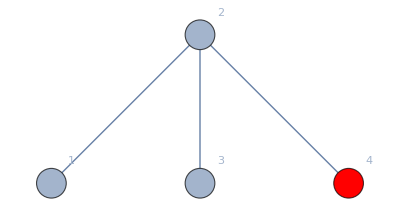
```mathematica
PauliActionCC[-Graphics-,3,p]
```

```mathematica
1//AbsoluteTiming
```

## User Interface

## Entropy and CI

```mathematica
(* presets for important channels *)
CHANNELGENERIC={q0,q1,q2,q3};
CHANNELDEPOLARIZING={1-p,p/3,p/3,p/3};
CHANNELBB84={1-2p-p^2,p-p^2,p^2,p-p^2};
CHANNEL2PAULI={1-p,p/2,0,p/2};
```

```mathematica
Clear[ShannonEntropyMult,CIMult]
ShannonEntropyMult[l_List]:=l/.Rule[0,_]:>0/.Rule[term_,mult_]:>-mult*term Log2[term]//Total
CIMult[λ_,λa_]:=(ShannonEntropyMult[λa]-ShannonEntropyMult[λ])/Log2@Total@(Last/@List@@λa)
```

```mathematica
Clear[CIThreshold]
CIThreshold[pa_List,p_,compile_:False]:=Module[{
targetFunction
},
If[!compile,
targetFunction=Function[p,CIMult@@pa] (* this scope conflict is intended *)
];

FindRoot[targetFunction[p],
{p,.04,.16},
Method->"Secant",
AccuracyGoal->9,
MaxIterations->1000,
WorkingPrecision->$MachinePrecision
]
]

CIThreshold[g_Graph,kSys_Integer,p_,symmetricSolver_:True,extraStabilizedVertices_List:{}]:=With[{
pa=PauliActionCC[g,kSys,p,symmetricSolver,extraStabilizedVertices]
},
CIThreshold[pa,p]
]
```

```mathematica
ConcatGraph[StarGraph[15],StarGraph[15],{2},1]
CIThreshold[%,VertexCount@%-1,p]
```

## Interface Tutorial

### Manual Export

#### Create graphs by hand

To create graphs by hand, look up the following functions:

```mathematica
AdjacencyGraph
SparseArray
PathGraph
```

Or directly use MM’s Graph object, where edges are entered with ESC ue ESC

```mathematica
Graph[{1<->2,3<->4,3<->5,1<->3}]
```

#### Create a random graph, add a hair, and plot.

```mathematica
CompleteGraph[10];
HairGraph[%,{10,9}];
graph=EnvironmentPlot[%,10]
```

#### Export instance

Just adjacency matrix for Full Solver

```mathematica
ExportAdjacencyMatrix[-Graphics-]
```

SGS for Symmetric Solver

```mathematica
ExportSymmetricCCInstance[-Graphics-,16]
```

### Automatic Export, Build and Import

#### Get CI for a Graph

Remove the semicolon to see full analytic expression. If you give “p”, that corresponds to giving CHANNELDEPOLARIZING where all the terms are equal; alternatively you can specify an array of four individual Pauli coefficients, e.g. {1-3 p^2,p^2,p^2,p^2}, or use a predefined block (see section “Entropy and CI” above).

```mathematica
CIMult@@PauliActionCC[-Graphics-,3,p];
```

For plotting, use e.g.

```mathematica
CIMult@@PauliActionCC[-Graphics-,7,p];
Plot[%,{p,0,1}]
```

The same graph is small enough to be faster with the full solver:

```mathematica
CIMult@@PauliActionCC[-Graphics-,7,p,False];
Plot[%,{p,0,1}]
```

If the symmetry group is 0, we cannot solve with the symmetric solvers; an error is thrown that you can catch.

```mathematica
Catch@CIThreshold[-Graphics-,6,p]
```

Solving fully still works.

```mathematica
Catch@CIThreshold[-Graphics-,6,p,False]
```

## Optimization Runs

Everything below can be safely deleted and is not necessary for the CoffeeCode interface. It contains some helpers for graph generation.

### Rooted Graph Product/Concatenated Codes

```mathematica
Clear[ConcatGraph]
ConcatGraph[g1_Graph,g2_Graph,v1_Integer,v2_Integer]:=With[{
vcount1=VertexCount@g1,
vertices2=VertexList@g2,
edges2=EdgeList@g2
},
With[{
vmap=If[#==v2,v1,If[#<v2,#+vcount1,#+vcount1-1]]&
},
GraphUnion[g1,Graph[vmap/@vertices2,Map[vmap,edges2,{2}]]]
]
]

ConcatGraph[g1_Graph,g2_Graph,v1_List,v2_Integer]:=
Fold[f,{g1,g2,v2},v1]//.f[{gg1_,gg2_,vv2_},vv1_]:>{ConcatGraph[gg1,gg2,vv1,vv2],gg2,vv2}//First
```

## Two-Level Tree Graphs

### Graph Generation

```mathematica
Clear[All2LevelGraphs]
All2LevelGraphs[n_,minChildSize_:2]:=With[{
partitions=Cases[
IntegerPartitions[n-2,{2,n},Range[minChildSize,n]],
{x_,xs__}/;x≥Length[{xs}]
]
},
With[{
head=StarGraph[First@#+1,VertexLabels->"Index"],
legs=StarGraph[##+1,VertexLabels->"Index"]&/@Rest@#
},
<|
"legcount"->Length@legs,
"graph"->Fold[f,head,{Range@Length@legs+1,legs}ᵀ]//.f[g1_Graph,{i_Integer,g2_Graph}]:>ConcatGraph[g1,g2,{i},1]
|>
]&/@partitions
]
```

```mathematica
Clear[GraphHash]
GraphHash[g_Graph,kSys_Integer]:=StringTrim@ExportString[ExportString[CanonicalizeByOrbits[g,kSys],"Graph6"],"Base64"]//StringReplace[#,{"/"->"-"}]&
```

### Higher Cat Codes

#### 5 in 5

```mathematica
HairGraph[ConcatGraph[StarGraph[6],StarGraph[6],Range@6,1],{1}];
graph5in5=EnvironmentPlot[%,VertexCount@%-1//Echo]
```

```mathematica
CIThreshold[graph5in5,36,p]
```